```mathematica
(23+24+3)/(75*24)
```

1/36

```mathematica
(35/36)^24
```

11419131242070580387175083160400390625/22452257707354557240087211123792674816

```mathematica
N[11419131242070580387175083160400390625/22452257707354557240087211123792674816]
```

0.508596

```mathematica
24*1/36*(35/36)^23
```

326260892630588011062145233154296875/935510737806439885003633796824694784

```mathematica
N[326260892630588011062145233154296875/935510737806439885003633796824694784]
```

0.348752

```mathematica
(24*23)/2*(1/36)^2*(35/36)^22
```

214400015157243550126552581787109375/1871021475612879770007267593649389568

```mathematica
N[214400015157243550126552581787109375/1871021475612879770007267593649389568]
```

0.11459

```mathematica
(24*23*22)/(3*2)*(1/36)^3*(35/36)^21
```

67382861906562258611202239990234375/2806532213419319655010901390474084352

```mathematica
N[67382861906562258611202239990234375/2806532213419319655010901390474084352]
```

0.0240093

```mathematica
1-0.5086-0.3488-0.1146
```

0.028

```mathematica
75*0.5085961238690968
```

38.1447

```mathematica
75*0.3487516277959521
```

26.1564

```mathematica
75*0.1145898205615271
```

8.59424

```mathematica
75*0.02799999999999997
```

2.1

```mathematica
8.594+0.028
```

8.622

```mathematica
38.14+26.16+8.62
```

72.92

```mathematica
38.14470929018226+26.156372084696407+8.594236542114531+2.099999999999998
```

74.9953

```mathematica
8.594236542114531+2.099999999999998
```

10.6942

```mathematica
(39-38.147)^2/38.147+(23-26.156)^2/26.156+(13-10.694)^2/10.694
```

0.897133

```mathematica
InverseCDF[ChiSquareDistribution[3],0.99]
```

11.3449

```mathematica
0.067*4+0.1+0.133*3+0.2+0.033
```

1.

```mathematica
0.067*(5+6+13+15)+0.1*8+0.133*(9+11+12)+0.2*10+0.033*14
```

10.131

Probability::argmu: Probability called with 1 argument; 2 or more arguments are expected.

```mathematica
Table[30*Probability[x==i,x\[Distributed]PoissonDistribution[10.131]],{i,5,15}]
```

{1.06259,1.79418,2.59669,3.28838,3.70162,3.75011,3.45385,2.91591,2.27239,1.6444,1.11063}

```mathematica
11*0.8
```

8.8

```mathematica
1.6444017165628444+1.110628919366545+2.2723940412476376
```

5.02742

```mathematica
1.0625862438852616+1.794176872800264+2.596686556905639
```

5.45345

```mathematica
3.288+3.702
```

6.99

```mathematica
3.75010976155528+3.4538510903924133
```

7.20396

```mathematica
2.9159137830637936+2.2723940412476376
```

5.18831

```mathematica
1.644+1.110
```

2.754

```mathematica
30*0.067
```

2.01

```mathematica
(4-5.453)^2/5.453+(7-6.99)^2/6.99+(10-7.20)^2/7.20+(6-5.188)^2/5.188+(3-2.254)^2/2.254
```

1.85006

```mathematica
1-CDF[ChiSquareDistribution[4],2.943]
```

0.567409

```mathematica
data:={{29.2,3040},{30.7,3840},{24.7,2470},{32.3,3610},{31.3,3480},{31.5,3810},{24.5,2330},{19.9,1800},{27.3,3110},{27.1,3160},{24,2310},{33.8,4360},{21.5,1880},{32.2,3670},{22.5,1740},{27.5,2250},{25.6,2650},{34.5,4970},{26.2,2620},{26.7,2900},{21.1,1670},{24.1,2540},{32.7,3800},{32.6,4600},{22.1,1900},{25.3,2530},{30.8,2920},{38.9,4990},{22.1,1670},{29.2,3310},{30.1,3450},{31.4,3600},{26.7,2850},{22.1,1590},{30.3,3770},{32.0,3850},{23.2,2480},{30.3,3570},{29.9,2620},{20.8,1890},{33.2,3030},{28.2,3030}};
```

```mathematica
model=LinearModelFit[data,x,x]
```

FittedModel[-2149.65+184.553 x]

```mathematica
s
```

s

```mathematica
Show[Plot[model["BestFit"],{x,20,40},Frame->{True,True,False,False},FrameTicks->{{Automatic,None}},FrameLabel->{"Relative humidity[%]","Solvent evaporation [%]"}],ListPlot[data]]
```

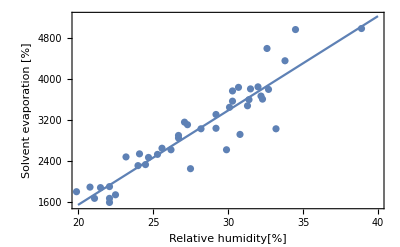

```mathematica
Datas
```

Datas

```mathematica
data
```

{{29.2,3040},{30.7,3840},{24.7,2470},{32.3,3610},{31.3,3480},{31.5,3810},{24.5,2330},{19.9,1800},{27.3,3110},{27.1,3160},{24,2310},{33.8,4360},{21.5,1880},{32.2,3670},{22.5,1740},{27.5,2250},{25.6,2650},{34.5,4970},{26.2,2620},{26.7,2900},{21.1,1670},{24.1,2540},{32.7,3800},{32.6,4600},{22.1,1900},{25.3,2530},{30.8,2920},{38.9,4990},{22.1,1670},{29.2,3310},{30.1,3450},{31.4,3600},{26.7,2850},{22.1,1590},{30.3,3770},{32.,3850},{23.2,2480},{30.3,3570},{29.9,2620},{20.8,1890},{33.2,3030},{28.2,3030}}

```mathematica
dataX:={29.2,30.7,24.7,32.3,31.3,31.5,24.5,19.9,27.3,27.1,24,33.8,21.5,32.2,22.5,27.5,25.6,34.5,26.2,26.7,21.1,24.1,32.7,32.6,22.1,25.3,30.8,38.9,22.1,29.2,30.1,31.4,26.7,22.1,30.3,32.0,23.2,30.3,29.9,20.8,33.2,28.2};
```

```mathematica
dataY:={3040,3840,2470,3610,3480,3810,2330,1800,3110,3160,2310,4360,1880,3670,1740,2250,2650,4970,2620,2900,1670,2540,3800,4600,1900,2530,2920,4990,1670,3310,3450,3600,2850,1590,3770,3850,2480,3570,2620,1890,3030,3030};
```

```mathematica
DataYTheo= dataX * 184.553 - 2149.65
```

{3239.3,3516.13,2408.81,3811.41,3626.86,3663.77,2371.9,1522.95,2888.65,2851.74,2279.62,4088.24,1818.24,3792.96,2002.79,2925.56,2574.91,4217.43,2685.64,2777.92,1744.42,2298.08,3885.23,3866.78,1928.97,2519.54,3534.58,5029.46,1928.97,3239.3,3405.4,3645.31,2777.92,1928.97,3442.31,3756.05,2131.98,3442.31,3368.48,1689.05,3977.51,3054.74}

```mathematica
Minuse = dataY- DataYTheo
```

{-199.298,323.873,61.1909,-201.412,-146.859,146.231,-41.8985,277.045,221.353,308.264,30.378,271.759,61.7605,-122.957,-262.793,-675.557,75.0932,752.572,-65.6386,122.085,-74.4183,241.923,-85.2331,733.222,-28.9713,10.4591,-614.582,-39.4617,-258.971,70.7024,44.6047,-45.3142,72.0849,-338.971,327.694,93.954,348.02,127.694,-748.485,200.948,-947.51,-24.7446}

```mathematica
SSE:= Minuse * Minuse
```

```mathematica
Sum[SSE[[i]],{i,1,42}]
```

4.60277×10^6

```mathematica
NumberForm[4.602768636916031*^6,16]
```

```mathematica
("4.602768636916031"×10^("6"))/42
```

109590.

```mathematica
model["ParameterConfidenceIntervals",ConfidenceLevel->0.9]
```

{{-2709.57,-1589.73},{164.705,204.4}}

```mathematica
model=LinearModelFit[data,x,x]
```

FittedModel[-2149.65+184.553 x]